# Female Satisfaction - Male Muscularity

https://twitter.com/datepsych/status/1741677937038913931 
The question is, how high is the sample count? This notebook is unfair BECAUSE I am assuming based on the sparseness of the dots, I assume each dot is one sample even though this is unlikely.
Also p-values seem to be totally useless. You run a Monte Carlo simulation, you can get any p-value you want!

-Graphics-

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,7,1}]
```

{1,2,3,4,5,6,7}

We do not have the total sample count. In reality, I suspect only 32 surveys were done. Time to multiply the sample count by 100.

```mathematica
Y={200,200,500, 800, 900, 400, 200}
```

{200,200,500,800,900,400,200}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution. I doubt that there are actually 32 points.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

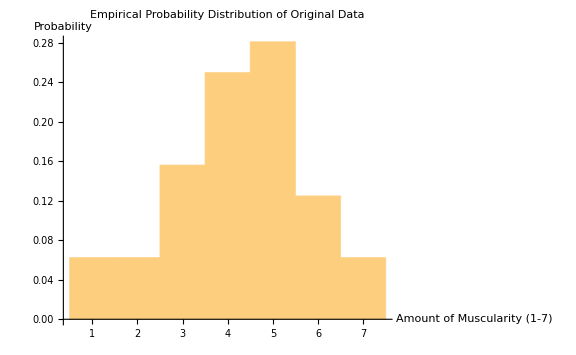

```mathematica
Histogram[ta,10,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Amount of Muscularity (1-7)","Probability"},ImageSize->Large]
```

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{4.25,2.77691,-0.272711}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{-0.319444,-0.272711}

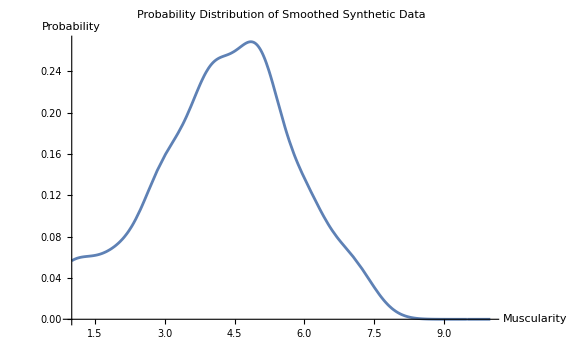

```mathematica
Plot[PDF[dist2,x],{x,1,10},PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity","Probability"},ImageSize->Large]
```

Muscularity of individuals apparently follow a normal distribution

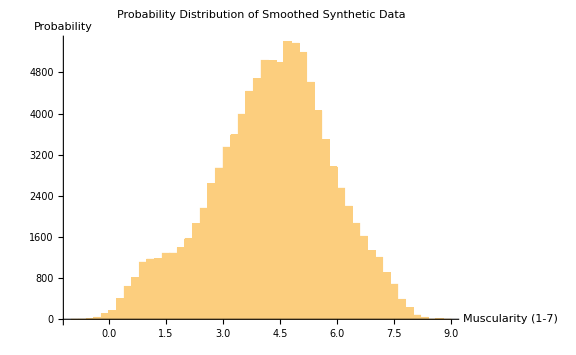

```mathematica
Histogram[RandomVariate[dist2,10^5],50,PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity (1-7)","Probability"},ImageSize->Large]
```

### Testing with No Noise

We find the gradient of a line.

```mathematica
(37-30)/7
```

1

From the picture of the graph, we derive this linear fit.

```mathematica
f=a*x+b/.{a->1,b->30};
```

Apply the regression line to the original function.

```mathematica
f1=f/.x->ta;
```

```mathematica
reg=Transpose[{ta,f1}];
```

```mathematica
lm=LinearModelFit[reg,{1,x},x];
```

Recall the table above was to get this linear regression fit of R^2=1 given the coefficients.

```mathematica
lm
```

FittedModel[30.+1. x]

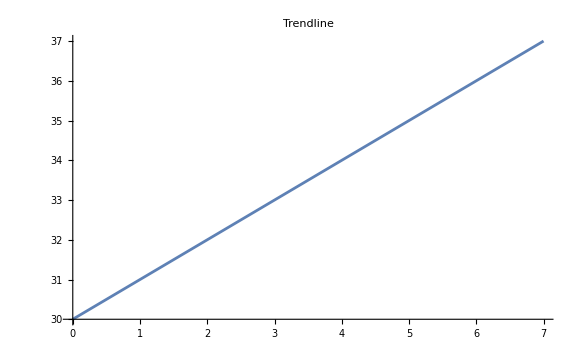

```mathematica
Plot[lm[x],{x,0,7},PlotLabel->"Trendline",ImageSize->Large]
```

Obtain the length of f1 based on the length of samples in ta.

```mathematica
f1//Length
```

3200

Apply some Gaussian noise to the function. Then perform the transpose to make it suitable for regression again.

```mathematica
reg1[sigma_]:=Transpose[{ta,f1+RandomVariate[NormalDistribution[0,sigma],Length[f1]]}]
```

Then, apply a linear model fit with the model. Check the p-value as usual, run about the model 10^4 times so as to get a distribution of possible p-values. This is the Monte Carlo simulation for possible p-value given a particular noise and eats up a lot of time. I have calibrate the noise so as to get the supposed p-value. Note that the noise to get the p-value is ridiculously high.

```mathematica
res=Table[lm=LinearModelFit[reg1[23.5],{1,x},x];lm["ParameterPValues"][[2]],{z,1,10^3}];
```

Get the assumed p-value distribution and parameters. The p-value is way too high.

```mathematica
{Mean[res],StandardDeviation[res],Skewness[res],Kurtosis[res]}
```

{0.00848935,0.0352191,10.084,135.635}

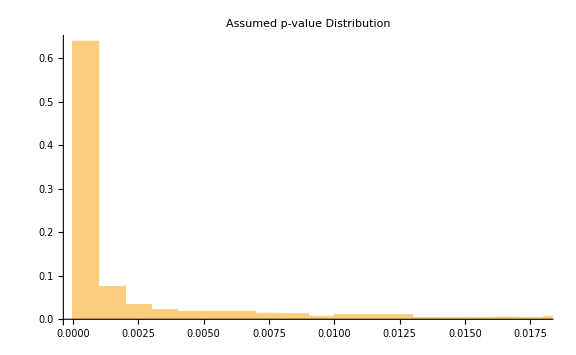

```mathematica
pl0=Histogram[res,Automatic,"Probability",PlotLabel->"Assumed p-value Distribution",ImageSize->Large]
```

Replicate the graph. From the empirical distribution. Note that I am being generous by assuming they had 3200 samples. Note that this is absolutely ridiculous, so the sample size is clearly must less than 3200. Note that to achieve this p-value, you basically have to far exceed the scale of the study in the first place as part of the empirical distribution.

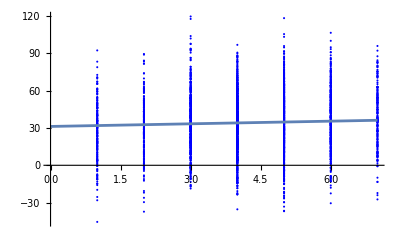

```mathematica
Show[ListPlot[reg1[23.5],PlotStyle->Blue],Plot[lm[x],{x,0,7}]]
```

### Replicating Their Linear Term

Apply the same technique, tabulate the values of the second coefficient, run the Monte Carlo simulation 10^4 times. We use purely the linear term.

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[23.5],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

Get the distribution parameters of the quadratic term.

```mathematica
{Mean[ta2],StandardDeviation[ta2],Skewness[ta2],Kurtosis[ta2]}
```

{0.987072,0.274979,-0.103697,3.09278}

Plot the histogram of the assumed quadratic coefficient.

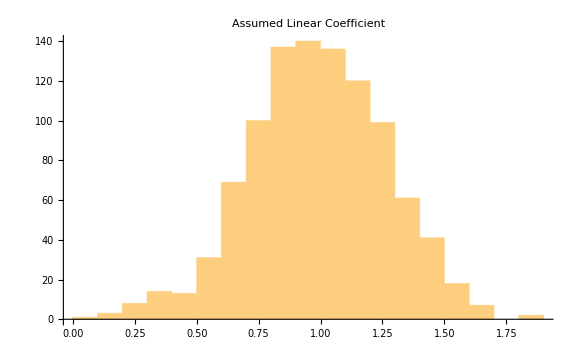

```mathematica
pl1=Histogram[ta2,PlotLabel->"Assumed Linear Coefficient",ImageSize->Large]
```

### Monte-Carlo of both the distribution and the quadratic term.

This is where you get caught out. If you have a low sample count, you should get basically nothing or no correlation. How is it possible that with such a low sample count they got such a distribution?

```mathematica
ta=RandomVariate[dist2,Length[f1]]
```

{5.06331,6.64308,0.0961114,4.3651,6.17042,3.19047,3.94001,5.19876,5.04384,5.043,6.97044,4.56344,5.95129,5.32963,0.953402,4.63854,5.25873,5.66706,5.16997,0.0743453,3.56777,4.62244,4.38914,5.07289,5.8455,6.06805,4.66881,5.53187,5.30566,3.8498,3.54554,5.16362,2.11963,4.7614,4.1663,5.98034,2.23098,4.25163,0.60208,3.20245,4.80257,4.41575,4.46491,3.09938,7.29883,5.5843,5.73789,6.0383,3.84339,5.61624,4.44232,4.57642,2.49634,5.02863,3.42868,1.0928,3.05408,4.83922,5.01833,3.96406,2.57468,3.1675,4.8135,1.09093,3.15262,5.24555,3.63415,6.71128,5.59786,4.42811,7.35845,1.39108,4.099,3.78159,7.36521,2.7398,3.2112,1.017,1.035,4.11439,5.56872,6.55995,6.01561,3.45244,5.092,6.01774,5.39312,4.77418,3.03949,5.91213,1.05982,2.72433,2.15934,5.01288,3.89632,5.44663,0.887279,5.48759,3.22083,4.48786,3.32417,3.96385,2.89515,2.3187,5.47928,6.40998,5.03236,4.00456,2.28171,0.764195,1.85313,7.30628,7.31637,1.25164,3.62217,6.28406,4.17451,3.71518,4.08979,6.68876,6.5951,3.43049,2.88872,5.52008,5.74315,4.20015,3.96246,5.77924,4.31505,1.13862,2.14191,2.11832,6.2098,5.36379,3.21672,6.44806,5.62733,4.20338,5.66335,5.98643,4.10823,5.00046,2.59195,6.82743,2.68333,4.44035,4.01369,4.59617,5.62003,4.74829,5.1893,4.1697,5.90162,4.57418,3.55356,0.490133,2.82525,2.31738,3.16063,5.16678,3.14068,6.87171,3.25576,1.15855,4.17716,4.00961,2.54836,5.13927,3.8488,2.95529,4.79557,4.90157,5.05086,5.01616,4.37543,1.68982,5.67658,5.78298,4.70245,3.37047,2.17186,2.85656,2.92888,4.73346,5.49366,3.96046,3.05102,6.19589,4.12675,1.98662,6.83553,2.69801,4.36642,2.67375,5.08926,4.09005,5.51449,5.53071,6.40803,2.41188,5.89647,1.54371,5.11968,4.74045,6.11797,0.997372,3.62072,5.38944,5.65403,3.13431,5.32341,3.46967,6.53015,1.97784,5.31252,3.59761,4.14524,5.09686,4.28091,4.41117,3.96152,6.35541,4.06267,5.3048,1.44753,2.66401,4.2662,1.57494,3.34297,1.67464,1.66745,3.54962,6.96729,6.85993,5.71601,3.805,5.01969,3.7067,2.65848,1.91976,4.26668,3.83096,4.14627,4.53413,4.21731,3.87717,3.01312,8.00039,4.11707,3.74669,5.40008,1.68383,5.25975,3.51662,4.20677,5.24584,2.79143,4.95255,4.2744,4.84764,6.00319,4.49237,0.351966,3.0913,4.58198,4.9991,3.94091,5.02104,5.85517,4.44548,5.87912,4.89791,5.794,2.71245,2.95931,5.47366,4.99577,2.26962,3.57981,4.35277,2.20347,3.37959,7.3478,5.30337,4.58446,4.84011,5.13663,3.07393,2.69282,3.26606,7.24922,4.22704,2.72943,3.72775,6.09102,4.77607,6.00642,5.20539,3.70838,2.62352,3.82289,5.69954,7.12762,5.13626,7.47775,4.05221,6.78026,4.89845,4.71121,2.6615,3.41022,7.03611,3.13154,0.719771,5.89759,4.62543,5.78306,4.98373,3.18737,4.76066,5.48769,6.27884,2.52263,1.97966,7.42455,6.93894,3.58494,4.35061,3.67035,2.65712,5.49744,4.25837,4.60892,5.8297,2.2521,4.98268,2.66366,6.45166,1.29474,5.54728,3.6341,5.3009,5.56936,4.99246,5.08381,3.66428,7.03628,4.69846,3.67555,4.41213,5.15507,3.59825,4.34612,4.57449,3.767,4.5408,-0.364598,4.20433,3.02146,7.82892,5.06503,3.33816,3.07258,7.41182,4.18214,3.86675,5.06029,2.50614,3.71958,4.07089,5.28942,3.95174,6.08668,4.31091,4.90941,5.65147,3.6363,1.68517,1.37101,6.99137,3.12955,4.59447,7.13624,6.18093,1.01606,4.66835,5.53081,4.4748,4.9641,4.64874,7.17627,2.40478,5.47977,4.98229,2.93312,4.65372,4.8268,4.36948,3.26608,7.15854,4.13905,3.10565,5.5818,4.79415,6.10852,6.55179,4.16895,5.73728,2.18616,5.00988,1.19963,2.96101,4.62551,7.29738,5.21908,7.08351,3.28755,1.26621,6.94952,5.00906,3.9489,4.19919,5.67376,1.90151,3.70407,4.72376,3.96438,5.03237,5.7117,3.51041,5.37418,4.56177,5.8407,5.25628,3.27887,3.43842,4.67796,6.43176,1.10048,5.20306,1.79587,5.19509,6.69587,4.39814,7.70355,0.815192,5.19674,-0.192364,4.53837,6.25471,4.86875,7.0961,5.02681,4.32239,6.38858,2.11119,1.11163,4.89696,3.71867,1.1062,2.84068,4.13645,4.34653,4.97451,4.29248,4.22524,1.96299,2.47199,1.28795,5.66507,2.42446,3.08599,5.07684,2.74024,3.75288,3.13506,4.82584,5.98252,6.77191,4.81695,4.02062,5.46809,2.73464,5.43311,5.37764,5.85897,4.12975,1.01228,3.78563,6.03053,5.73183,5.22109,2.41467,4.61544,5.22159,1.94486,3.27173,6.69041,3.93212,5.27941,5.78778,5.70075,6.09056,4.29923,5.23326,3.16828,4.31898,3.57439,5.40292,6.69253,1.52277,5.83881,3.82187,3.68961,1.57253,5.47114,1.15522,6.69329,3.47604,2.61607,4.79161,4.50051,3.00881,3.90698,4.32376,2.72928,5.27516,4.14408,7.19342,4.66682,6.63727,3.09128,5.41936,5.15793,0.520494,3.18824,5.90632,4.48229,3.24934,4.09259,3.71824,0.833039,0.962959,6.39786,6.09772,0.784546,6.47517,2.88181,7.09388,2.64018,5.27976,6.51465,3.7827,3.53179,3.25153,5.67784,4.14709,4.43314,2.74965,5.31166,5.34022,5.54571,3.38885,4.01401,5.93113,7.31365,2.8922,3.70212,6.04989,3.24493,3.60114,4.33676,3.70129,5.3532,2.91203,3.89351,7.95078,3.75461,2.84139,4.56985,4.68536,5.91271,5.71379,4.76957,3.73348,2.45672,7.77224,3.48226,5.11539,4.51022,6.11366,4.62556,2.52424,5.7879,1.37985,4.26538,7.29356,5.91945,4.57857,4.40048,6.77926,2.46927,3.23252,4.61478,5.59143,4.2911,3.95366,2.43109,5.14167,4.6621,0.897421,6.53622,4.37878,6.42837,4.32479,4.03316,3.38743,4.23946,4.32431,1.1535,4.37164,4.64594,6.3442,3.50852,2.73249,5.56625,2.75372,1.1851,7.06572,0.850931,5.55324,4.67476,6.09597,4.91018,3.10768,4.87797,6.76501,3.20632,1.70893,4.6125,5.26712,6.32303,3.80367,3.15029,2.72955,2.46845,3.06882,3.55457,1.74775,3.55727,5.74663,4.55063,5.18746,6.38346,3.95521,6.23747,2.07815,4.68251,5.34316,3.57847,2.71096,4.45655,2.64176,1.74925,5.60733,5.7144,6.28409,3.87873,2.70713,4.81574,4.76694,6.40776,5.14168,3.01607,3.47983,4.03161,1.88953,3.82903,4.09248,4.4516,4.62056,7.02013,5.03591,5.02335,5.23943,6.42626,2.47419,3.50207,2.21114,2.95193,4.97561,3.89765,4.37681,4.63027,5.65579,3.28484,2.73437,7.05105,4.49661,0.503945,1.95566,4.46157,7.23305,2.88013,3.68645,4.26675,4.73512,5.70253,4.03377,4.86423,3.88818,2.4581,6.37809,6.0562,4.83367,6.52671,4.73531,0.96949,2.74019,2.91123,3.98388,6.64099,5.90266,7.35678,5.30374,3.63723,4.63784,4.30051,4.17791,3.8054,6.29586,4.53497,4.33549,6.711,2.96799,5.57023,0.794001,4.23225,4.321,1.14265,3.94293,4.30785,2.23652,4.92904,4.91617,4.12711,6.16714,6.17016,5.46831,3.02257,4.12493,4.66003,4.67413,3.61671,3.54553,5.77711,2.10765,4.07304,2.88916,6.0086,6.27181,3.821,3.56671,5.73301,3.95854,4.35028,4.90657,4.5017,5.02148,3.78836,0.42692,3.99101,2.21518,0.213256,2.90931,3.64303,4.78461,3.14517,5.88746,2.5438,6.68172,1.95575,4.72834,4.17365,4.02299,4.51527,5.15137,0.366484,5.92414,4.66282,4.69687,6.51268,4.71302,4.85251,1.08591,4.75163,0.369803,2.59331,3.82758,6.44131,4.85256,6.61844,2.45262,5.08629,6.08133,2.58781,5.27818,5.2642,2.66644,4.49314,5.64473,3.41653,1.66072,3.08971,6.58793,4.6326,5.3194,1.94477,6.40985,4.78095,3.46218,6.37541,4.01667,1.28405,1.05903,4.22807,6.35033,5.08224,4.90836,4.68864,6.88588,2.70586,3.94453,0.857556,3.01378,0.598146,5.98023,4.17007,5.12627,5.60257,5.06942,2.96636,4.0809,3.22833,5.55405,4.93369,3.24692,3.69272,1.34822,4.85175,4.72421,2.5531,2.13599,2.07181,2.34661,6.2277,3.52909,7.11717,4.11407,1.72332,5.86067,5.32363,3.5209,1.64338,2.83523,0.722867,2.40042,2.48881,4.94153,3.17013,2.86531,2.34221,3.55958,4.24899,2.61858,1.62733,0.285909,4.15277,4.35982,0.0943962,3.26974,5.53446,2.57032,3.9498,5.53616,4.04118,3.54438,6.07023,5.67397,6.39332,3.38574,5.82255,1.98374,5.63818,4.92394,7.84133,3.68158,5.55681,0.810131,6.87182,5.94386,2.95775,5.11122,3.19248,5.00254,4.65405,0.952947,5.00026,5.82684,5.65783,2.29389,3.79588,4.53249,5.3816,4.62314,2.92268,2.23551,5.74441,1.83496,2.59278,6.70502,3.68766,6.30464,5.22761,3.20297,6.21281,7.57996,5.74548,2.47118,2.69118,4.8432,2.41763,5.40117,5.58113,4.68457,6.85979,4.87678,4.86002,3.81657,6.20858,7.335,4.35357,2.95591,3.49111,6.68868,6.00385,4.02321,4.04644,2.93512,4.46275,1.70101,6.27276,5.65523,6.31685,5.20608,4.74784,2.08496,4.84686,5.85876,0.837263,5.93714,4.67085,5.67098,4.32596,1.2685,4.2668,6.3442,3.29822,5.21332,2.86958,5.34381,2.2012,2.3413,3.09881,3.82072,5.85258,3.39794,5.25293,5.54533,2.57695,5.14086,7.6309,7.4763,3.976,0.623378,3.89708,4.33153,1.32719,5.0911,4.18365,2.43424,4.00421,5.26806,6.50916,0.33676,3.36531,1.34769,4.95041,3.92632,1.56623,5.56755,3.77917,2.03324,4.99413,0.548245,6.46567,6.2438,0.90834,4.68294,6.51997,4.16072,1.39067,5.4518,4.65321,4.68913,7.26025,6.45773,5.09359,7.31482,4.73771,5.49899,4.68088,1.85561,2.69838,2.01428,2.78332,3.75201,6.48176,0.471513,6.34867,1.67672,5.92598,5.48049,6.03806,2.59387,3.59508,4.271,3.46851,5.1198,4.72019,3.01046,6.82305,4.19958,0.845896,4.66605,4.09919,4.00144,4.09177,4.07505,0.201956,6.27139,4.65761,4.08022,4.83782,4.38311,6.78088,3.80307,6.23465,2.81193,3.29262,4.81243,2.82232,3.72428,5.1599,2.9371,6.66609,4.06714,7.15912,3.94114,3.62066,6.1329,6.84822,5.99259,6.37506,3.1599,3.24583,1.50289,2.10959,5.13341,2.24748,3.42314,2.59508,3.83541,4.2156,2.90587,0.722103,3.74732,6.09393,6.21752,4.1363,4.63947,4.72724,4.54239,5.19554,3.99674,4.07999,3.52826,4.93933,3.4367,0.377015,4.5624,4.85605,7.03578,3.68675,2.60976,5.40506,5.02102,4.752,4.1992,3.07203,4.10281,3.69727,5.96212,6.72813,4.48074,7.51553,6.64054,4.13493,6.23548,3.99442,3.76423,0.377472,5.39573,4.64419,5.54271,5.44969,3.99449,4.23574,2.34922,4.68967,3.27774,3.17086,0.62245,6.09802,4.29962,6.84346,3.64359,5.92292,6.08359,6.51819,3.59474,2.41954,3.74169,4.19662,4.61915,0.44492,2.9007,4.66298,4.01809,4.37946,3.05973,5.40421,3.32889,3.3122,5.74299,4.97674,5.21528,3.92449,5.05717,4.46803,2.60104,4.61831,3.54836,4.46603,4.83808,4.95666,5.38527,3.36763,3.76735,4.88578,2.84139,5.52818,3.41378,0.0992534,3.85074,4.61701,3.39147,3.79227,7.79626,3.35526,1.65525,4.0137,4.96993,3.97461,4.5904,6.21083,4.71807,5.76178,2.73537,7.29463,0.00529107,7.45121,0.486173,5.70641,5.56418,5.2811,5.05781,3.26186,4.79337,3.73926,4.88554,4.30133,4.71858,5.42456,3.07042,3.97106,4.96349,6.92692,2.22842,4.87449,0.474764,4.59008,4.86161,4.60104,4.98801,4.07953,7.22341,4.11876,3.88225,5.11867,4.31223,4.26848,2.83379,3.18565,2.68914,5.10813,6.40292,4.91475,0.661991,4.47863,7.19405,2.10515,3.63221,5.35181,6.35275,7.10145,6.06475,3.89052,7.82748,3.72661,4.91955,1.48192,4.15578,2.08679,2.85486,3.27828,1.59382,2.32871,5.82033,1.31885,3.60659,3.56947,0.735308,5.63271,4.08592,3.89402,4.85152,5.31197,3.99503,1.10874,2.46229,6.04455,4.13694,5.40377,7.75295,3.14436,4.12333,3.17555,3.57016,4.53479,4.51749,4.39615,3.68059,4.97195,4.39091,5.28912,2.03416,3.73335,5.37204,4.9259,6.9105,3.29773,5.61439,2.30602,3.69553,2.9241,4.11899,4.36403,2.72898,3.83377,3.47266,2.66995,4.76178,2.40866,3.98515,4.35364,5.86532,4.00026,5.21699,0.442404,3.46609,2.02133,3.48364,4.36851,4.97267,6.50824,1.83376,0.956672,2.08127,4.48139,6.70955,4.73333,4.54887,3.85632,4.41501,3.57334,3.91099,5.06136,5.59583,5.00884,3.50685,1.21089,4.71718,6.38946,6.22685,6.88469,1.94222,5.28606,1.9915,5.25034,4.29716,1.44331,5.06278,3.89071,4.45153,1.58804,4.58725,4.71665,3.58448,5.27751,4.70475,4.04138,5.23206,4.68203,1.38684,5.57845,4.64399,7.36565,5.00985,5.23686,5.72314,3.76108,5.32336,5.17056,5.68852,6.17601,2.59075,5.50896,3.28853,5.63156,4.39141,0.755393,3.47661,5.02796,6.17373,1.07805,4.44478,5.04884,4.98387,7.61678,3.24361,5.29618,6.95259,6.51197,1.84602,5.94876,5.41018,6.16328,3.71484,3.43821,5.56043,2.00396,5.79825,1.21692,5.7179,6.71565,5.44012,3.6423,0.942491,5.35541,3.29224,4.92209,5.04076,4.39599,4.61449,3.83232,4.22358,2.98165,6.3585,2.64133,3.80905,3.98135,3.2602,4.7477,4.5842,3.27082,3.06838,5.75034,5.27826,2.44368,3.9965,3.55274,5.94825,7.21783,3.76388,5.10796,5.03887,1.26365,2.87777,4.39675,4.74976,5.96222,4.21208,2.20816,4.03261,4.22256,3.25499,2.90392,4.56423,3.67561,4.64885,4.53663,7.17481,2.95391,3.40671,3.24061,3.80103,5.79856,5.00075,4.55851,1.1269,2.8774,5.46568,3.00515,6.94883,5.65355,3.76976,2.58669,3.11144,3.44482,3.56184,3.90742,4.78297,4.79177,3.07376,4.21929,4.62625,1.50356,4.60155,6.22574,1.94905,2.47763,5.27571,6.32129,3.79553,2.45995,3.31764,4.14878,2.40428,1.2595,2.92326,5.76273,4.54115,4.31838,5.76686,1.24565,1.19856,3.30438,6.68334,6.7758,5.51799,5.58578,5.92672,5.49374,0.797584,7.00103,3.3934,3.80725,7.10684,5.34967,5.59009,5.39234,2.74651,1.87251,3.13464,4.29911,4.06273,1.62104,4.36408,3.05701,5.1763,4.41936,4.29147,5.71222,6.11698,5.01265,5.3005,4.9991,3.15168,4.80265,2.43633,4.25569,2.87444,6.71396,3.46844,4.96572,7.21345,3.33401,1.64214,7.5329,6.05522,5.28692,3.95392,5.63685,3.26576,4.877,5.00075,5.99918,5.06632,5.12269,5.44506,2.3995,5.70566,5.663,4.44423,4.21445,5.10956,2.23895,4.13435,4.29094,7.13127,4.95293,0.766482,5.3193,5.41715,5.0616,4.20056,4.00839,5.35674,4.895,5.1984,6.98872,2.71938,4.82652,3.83909,1.47017,2.03582,4.99628,5.35981,-0.388337,5.06174,5.53696,5.84421,3.86706,2.92371,3.39353,1.62594,6.54724,0.648102,5.30524,7.15889,7.89775,3.62434,5.71849,4.36183,4.22146,4.89214,5.63243,1.26516,3.78825,4.74924,2.32836,3.94957,4.02826,5.91522,5.12917,4.85048,4.46057,2.26474,3.09917,3.35764,5.51289,2.48615,6.27236,2.58552,4.87419,4.71013,0.906976,2.73973,5.42121,1.39336,3.93775,5.68326,3.68844,2.58167,1.91505,4.93663,2.76592,1.75237,5.36374,4.22111,5.22884,4.06781,4.18588,5.76464,-0.161668,4.96257,6.37402,5.03017,5.44724,4.07342,3.66718,4.75159,2.84203,6.22051,4.21349,2.0957,4.36177,4.6488,4.5789,3.58294,0.332373,3.80094,6.26978,3.05782,4.12325,0.557408,5.16415,4.00322,4.40941,3.93376,0.290234,0.93464,4.78148,5.75035,5.17055,1.65437,5.35232,4.49939,2.62868,4.63947,5.74857,3.08152,3.55004,2.54309,5.77856,4.04633,3.86244,5.37608,4.14568,4.09936,4.25035,5.00965,2.30186,0.894693,6.79427,6.02956,4.5982,4.42713,5.89936,5.26513,4.77597,2.70846,5.57647,5.59929,4.53076,3.06599,3.85912,3.88514,6.05704,4.19092,3.39017,4.41718,3.43944,7.43901,3.81485,6.09312,5.13589,0.350364,3.74571,4.14018,3.19986,4.65329,3.09479,3.31522,4.28541,4.69507,5.51125,5.87696,4.02019,1.76473,3.8116,2.50451,5.44619,7.68229,6.90983,2.68055,3.08967,6.68635,1.99223,4.10806,5.51184,2.98707,1.55875,3.96688,5.05659,4.87745,2.77466,5.57686,5.20889,4.86607,6.0553,4.42672,5.11723,3.6715,3.51693,4.83467,5.73357,4.17232,2.16571,5.45305,4.1213,6.15217,1.93082,5.84855,3.31405,4.39584,4.43133,7.04183,7.29046,5.87819,3.9634,4.52469,3.44527,3.94734,2.11879,5.52782,2.88046,4.78399,4.20599,2.98002,4.15934,3.39608,5.0399,5.62851,1.25978,3.67749,7.45968,3.85589,3.02973,5.3571,4.54469,6.12034,1.48167,4.64232,7.39236,7.83598,2.37723,3.47822,3.29486,6.92596,2.79081,3.55036,3.38006,3.06997,6.01342,5.96259,3.34357,6.74332,3.16122,1.25051,5.22163,2.36018,4.75926,0.876479,2.02438,5.48925,4.48362,2.92694,4.19137,7.22272,4.99477,5.63312,1.34233,4.39139,4.25343,5.69148,5.49731,6.18773,4.59617,3.87565,6.12085,3.98693,5.39209,4.46482,4.03472,4.03617,5.72093,1.86047,4.62113,4.307,2.81549,3.78245,4.69598,3.39717,5.14317,5.96989,2.6419,3.39941,4.54804,5.07835,6.38797,3.88106,1.81826,4.83061,5.22646,4.14817,5.21449,6.06449,4.60469,3.94238,4.01025,4.15957,7.24467,5.0285,6.05087,4.55102,6.00125,6.32855,3.64079,4.23049,6.56884,5.67897,4.70351,3.6492,2.7896,3.99195,2.27521,4.73449,4.85299,2.56176,5.12129,0.17916,4.76549,6.09548,5.59588,6.73061,2.88286,4.04316,2.3789,1.07459,4.66782,4.08166,3.60551,4.6404,4.54695,5.41599,2.92697,3.91424,3.94283,3.32453,3.09571,4.68862,4.74827,6.30307,5.00311,1.5221,5.07562,0.0127053,4.97133,4.34334,2.85892,4.95032,4.31156,4.25605,3.85421,5.66337,2.93654,6.05728,4.36326,2.69797,4.97854,3.781,3.28312,6.61271,2.53505,5.75519,4.60735,4.81524,5.12585,5.6999,3.50072,7.29349,6.14594,6.06936,0.999107,5.92176,5.02046,4.49492,4.78295,0.422815,1.03807,0.504021,6.99474,3.61922,5.35937,3.25133,4.38081,5.18786,3.44163,4.18513,3.30159,6.20097,3.81679,4.20556,4.02239,3.3702,3.66132,4.96336,5.63794,1.61565,2.14866,3.89127,3.35293,4.06025,3.90092,6.36682,4.04644,4.02438,4.56119,6.62648,5.58683,1.55299,2.78711,4.92479,4.64605,6.73684,1.55981,0.578723,6.79663,2.0281,2.67823,2.42201,6.59719,5.10312,3.78498,4.34637,4.74268,3.90093,3.9068,3.66317,2.03629,5.4591,3.6232,6.54,3.39107,6.84016,3.03947,0.946294,4.68899,5.61913,5.11741,3.61375,3.06673,4.22248,3.83737,6.00423,2.08383,4.66055,6.3972,3.28899,6.84507,2.53453,0.0582072,1.22337,2.35359,3.0774,4.0707,6.34341,3.69144,2.09416,5.45221,4.63478,6.72555,3.28976,5.03469,4.7963,3.85955,6.1029,4.18689,5.81898,3.88269,1.39164,5.02218,4.31026,4.366,6.50006,4.19177,3.7781,4.73648,4.94841,5.44424,4.91846,3.63913,2.05079,3.07396,6.07106,4.69834,2.55036,5.76613,4.61246,5.77315,4.24716,6.39605,7.40847,5.18416,3.26975,4.72865,3.75311,2.37956,3.93316,4.34581,3.91395,3.38492,4.02733,3.16478,6.51269,4.63903,2.78966,6.58646,4.15567,5.72451,3.95629,0.61843,2.0756,3.66007,4.94833,6.48711,7.40114,7.19703,2.90452,5.6987,5.58955,5.75015,0.99184,4.57864,3.48855,3.15194,0.0517645,7.34982,4.20189,2.61852,4.66736,3.81297,6.82015,3.93164,1.62829,5.72066,4.2418,2.90692,5.23326,4.94498,3.35035,4.91333,5.30854,3.06708,2.84951,4.49782,2.75708,3.53047,4.56558,3.07726,3.6641,4.54771,4.41268,6.42785,3.76315,3.04931,5.85118,4.1993,2.40677,5.17424,3.19722,3.89902,5.92776,1.36159,3.86028,0.165509,5.53852,4.2696,7.43445,5.61263,5.53915,4.23699,4.50372,5.24316,4.02839,3.63927,4.57941,5.4839,0.922932,3.9674,3.48741,-0.0717974,4.05332,4.97292,6.94571,6.10191,3.81568,0.403687,3.67974,6.06252,3.18378,2.40598,4.28673,5.81823,2.48113,5.27801,3.39209,4.22093,4.03867,4.60547,2.229,5.32699,3.19265,1.2739,4.0106,7.18397,5.83517,1.70973,3.58362,3.62567,5.06265,6.39744,5.72873,4.52147,4.77829,3.33884,5.13689,4.11454,1.19838,1.80779,3.21553,6.32818,4.48903,5.52159,4.72557,1.83133,5.18205,1.88606,4.71504,6.77762,4.25195,3.69792,4.69307,6.35984,6.8915,4.30504,4.71183,4.19897,4.6056,1.76775,4.37453,5.09566,4.14431,2.66613,3.83944,1.67811,6.60762,6.07523,4.71109,5.64888,6.26134,1.65047,5.29142,5.78489,5.48689,4.79743,6.85136,4.69135,2.65435,2.9604,5.12903,3.57099,5.82094,2.54709,4.33565,1.53556,6.78426,0.42726,4.6978,5.03513,3.50507,5.62121,4.40631,5.30984,3.38234,5.37501,3.95814,5.74577,6.74692,1.28475,3.72038,2.04732,4.66165,3.24472,6.3217,5.94687,4.8186,1.54358,5.23541,7.71688,7.13587,2.90362,3.12962,4.78166,4.37336,5.95446,4.59916,6.54454,3.47739,3.39993,7.94595,6.74676,4.41091,2.36608,6.69009,1.59756,5.67577,4.30272,3.47702,5.51159,3.77271,2.36088,4.86639,1.13392,5.91175,3.58396,4.50829,4.32301,2.49435,4.95221,5.68943,3.78111,5.51592,3.09684,4.05395,3.68077,7.62376,4.77581,4.2498,2.75674,1.41448,1.9302,3.7812,1.55448,2.95772,3.61197,5.11477,6.15556,3.87605,4.11675,3.10194,5.10138,4.04428,4.81608,5.7927,5.12979,3.73001,4.96663,3.42892,0.190775,1.60544,2.24997,5.89965,0.834947,6.79387,2.01116,6.05088,4.39426,3.91857,0.0947975,5.32783,5.13985,5.65749,6.41503,4.37251,2.14485,5.36766,6.7362,4.23728,2.81422,3.09999,3.65074,2.43172,6.37961,5.8602,2.82114,4.57225,6.17675,5.18341,3.56965,3.10798,4.59256,3.53185,5.31229,4.88114,5.08272,3.111,5.96837,2.79025,5.13259,1.79403,1.11519,4.40431,6.83022,6.64613,3.90825,3.75048,5.227,0.254593,5.69832,5.29778,1.24875,2.19914,4.60451,5.38976,4.75658,5.1873,5.74653,1.74124,4.80316,1.96538,2.87935,1.34234,4.55136,2.19083,6.34413,4.54496,5.28531,6.14471,3.17229,3.42999,3.67713,2.3338,4.32995,4.70139,4.10308,3.42277,4.62331,3.13539,1.51704,2.50509,6.27018,3.5954,5.65888,4.17763,2.08864,4.68348,6.67317,4.70807,4.9381,6.50871,3.86084,6.57038,4.80213,0.998062,4.83212,7.24185,5.51633,3.52387,3.21125,3.8654,6.52591,5.39221,1.48182,4.34357,3.47693,4.70368,5.10739,5.65882,4.13814,4.28028,4.66302,3.70836,3.98832,3.90232,5.35116,5.13924,5.69738,2.16466,4.43555,7.05354,3.33663,0.155299,2.85805,5.20299,6.12819,5.61976,5.7901,4.3346,3.54795,3.71967,3.76482,5.26584,3.05315,5.8116,5.50754,4.68811,4.42269,4.8244,7.05604,6.32948,5.12543,4.64998,4.78179,3.55416,3.36031,4.95967,2.47961,4.25217,2.32612,4.01123,4.06443,0.372185,6.84871,5.10238,5.86917,5.2582,3.28893,6.55739,4.08077,3.1639,6.66713,4.92588,2.7792,4.34206,6.68526,2.08587,1.54893,4.09298,3.09113,5.14868,3.76553,2.8654,2.48867,5.38192,4.69972,7.4312,5.19521,5.06587,5.31507,3.54561,5.10268,4.36619,4.23947,5.44044,4.28437,4.03747,6.21863,5.83609,7.12844,2.60288,2.96697,6.48871,3.04164,4.49007,4.96632,5.55648,4.62978,2.23179,2.72122,3.79458,3.55516,4.32703,7.95541,4.59596,4.95345,4.42372,6.93595,6.80407,4.098,4.1168,4.59539,2.71836,1.0653,2.65136,3.92371,1.23388,4.06494,2.61729,4.9929,5.01331,3.48599,4.6973,4.77795,5.27595,3.36444,4.06057,6.96884,7.51125,4.88457,1.27967,3.77119,5.22751,3.19365,3.34342,4.46169,2.22936,3.90096,4.81924,7.37291,4.66564,7.24622,3.34877,4.05862,3.51341,4.93937,4.37364,1.98555,4.64122,1.75606,5.48037,6.04073,3.97646,3.46839,4.9965,1.23957,1.98634,3.87953,3.31379,2.9919,0.269116,6.12981,4.51542,3.94587,4.26357,3.39655,5.36225,5.44971,3.28853,5.89552,3.1742,5.52766,3.20997,5.05797,6.3574,3.55759,4.45096,6.13867,0.734149,6.11809,5.09128,4.0138,6.18788,2.46633,5.43394,2.72889,0.887506,2.65011,3.34522,5.1466,6.32786,6.62879,5.89652,3.80953,3.54927,2.96642,1.17231,6.63949,3.30333,4.99559,2.41613,5.88262,4.48034,4.56802,5.49722,4.49723,3.75537,4.90756,4.16652,4.28973,5.23943,3.76195,4.61995,5.0765,5.45847,6.24444,3.82045,4.16574,5.24971,4.51858,0.964777,4.41501,7.44414,4.01542,6.0461,5.48496,3.3631,4.52173,3.16692,2.21332,7.18323,4.68482,4.56334,5.60342,3.90712,5.83314,5.36439,4.11272,3.31653,4.55317,6.34189,5.66356,5.46327,5.99571,4.21953,4.67158,4.85948,5.27275,4.26104,4.78743,1.68547,5.72334,4.97838,4.32391,2.98564,6.93249,5.40097,4.6383,3.87531,7.56092,4.70915,4.30157,2.7146,2.58079,3.99564,5.92457,5.68342,5.59541,4.42334,3.31604,7.13012,6.16656,5.46588,4.52544,2.23751,6.12534,4.34548,3.2767,2.63811,3.32689,4.37948,5.76723,1.62811,5.86786,5.31167,4.57515,1.10896,5.11447,4.79535,2.19244,1.69764,4.55765,0.71885,1.89556,4.79008,3.21029,0.549299,3.53954,5.222,3.06028,3.86681,3.59336,3.8954,2.19778,5.29764,4.13723,3.81306,3.23765,1.15825,4.46202,4.33179,0.470438,7.37949,5.55403,4.72199,3.15877,6.2106,4.61984,3.83287,2.39694,3.55718,7.06245,2.35139,5.01875,4.75518,5.54799,5.93552,4.8657,4.66624,4.03168,4.63312,6.38713,2.3135,2.59776,5.47259,4.12147,4.11741,2.86082,5.87488,6.04617,4.33281,4.24014,3.45606,4.93583,4.26813,5.4788,5.00121,4.8695,7.19651,2.36963,2.73871,2.94975,6.22066,4.50816,4.07418,4.30271,5.78558,4.16981,5.55616,6.28568,0.503502,5.19192,6.19743,6.74787,7.2406,3.08306,5.48042,3.44417,2.37502,4.5713,7.13915,6.10508,1.34747,0.684183,3.94679,6.13867,3.75272,3.7424,5.61979,3.92079,3.01636,4.80233,3.95786,5.79471,3.11253,1.6044,2.65353,5.83036,4.96975,0.484897,2.56902,3.50267,1.77165,4.4211,5.85201,6.12633,0.962503,3.72773,4.00983,0.577802,4.57573,0.209167,3.58333,2.59451,1.50147,3.16255,5.60777,4.72622,1.02813,7.12018,1.15598,5.96296,3.92092,1.50595,5.32833,5.65003,3.57279,5.13473,6.23222,1.42301,3.92199,3.19273,5.64929,5.31421,5.57656,4.83583,3.27093,3.31992,2.7525,3.29025,3.19597,3.82172,4.23499,2.17612,1.92665,3.77637,3.70455,3.40994,6.28579,4.40024,3.47417,2.84493,3.20076,0.725692,4.27809,3.95673,5.30212,3.12178,6.6432,5.49664,5.40611,4.70547,3.83057,4.04632,5.42879,1.19747,3.65805,3.57541,6.2478,5.24419,5.03481,6.05834,5.69231,6.80483,1.53845,3.74028,4.02247,5.47897,5.34631,4.46613,2.91247,1.19274,4.29312,5.35842,5.40619,0.587875,2.61895,6.07475,7.04262,2.94836,5.17761,5.97388,5.35177,6.84175,5.70783,5.79243,4.72183,7.42604,5.35726,5.03044,5.06974,3.69083,5.5428,3.97705,1.93463,5.33044,7.11467,2.372,6.39624,7.04974,3.70945,0.347264,4.89668,2.24487,2.09319,4.70705,7.63764,4.80825,2.65938,4.6114,1.10168,2.06882,4.12897,5.12851,8.18788,3.00381,5.02048,-0.149199,4.3577,1.23904,4.41639,6.6554,6.73399,6.57643,5.60296,3.90882,3.55974,5.21416,5.61301,3.77763,4.96501,5.98786,3.56537,6.80888,3.52042,5.93767,5.12982,3.0552,6.8137,3.50777,6.0138,0.948479,3.10499,5.46177,2.44006,5.06353,4.89017,5.28072,3.75949,5.10501,1.30945,1.94952,4.90066,5.17217,5.55974,5.00265,4.2799,5.49977,6.24732,5.46381,3.99205,4.24555,4.96378,5.07006,6.44432,3.70752,3.56127,7.62315,5.01467,5.62879,1.99954,4.59614,2.77227,1.88168,5.37243,1.10486,5.54925,4.2366,2.46999,1.7589,4.53108,4.80274,2.47863,7.5048,2.83651,4.95163,6.27155,3.11858,5.94414,3.8145,3.45951,6.10063,6.79471,1.99164,2.29476,3.37234,4.13445,3.88605,7.17232,4.5369,0.723863,3.95509,6.66313,5.6733,2.57147,2.54086,2.43822,3.76045,2.38381,7.27468,7.61722,7.05899,5.65486,0.104388,3.02812,1.2938,3.76008,5.86241,5.07296,5.29111,4.28202,5.26789,5.91145,4.76852,4.97381,6.17091,4.82964,5.03926,3.94378,2.67631,0.652666,2.45001,3.09297,3.05232,2.25186,4.20624,1.42,4.20217,4.59147,5.4353,4.82798,4.93509,4.66487,5.71855,3.7528,6.61326,6.48585,1.75221,4.9209,6.02633,5.04791,2.47204,5.07441,1.9559,5.74316,4.81399,5.29497,3.53783,6.37174,0.637635,5.29772,2.09296,4.12801,6.36849,7.29638,2.73796,2.98187,4.12266,3.10753,4.35715,3.81981,3.94762,1.76138,2.86653,0.739936,3.85182,3.63648,5.68804,2.30921,5.48104,2.59994,2.89955,3.96763,2.63871,3.61221,5.3483,4.90242,3.71037,3.70233,4.19163,4.32594,4.59632,1.52379,5.21901,5.05462,3.95862,1.30458,5.39568,5.30286,3.82231,4.86023,4.24325,3.66175,3.53781,5.30167,1.61037,3.81399,4.06523,3.52432,2.69631,5.15969,2.82663,4.65361,5.9996,2.40141,4.76369,4.36935,5.59517,4.80863,5.5472,0.849369,6.60936,4.95176,3.78388,3.93138,6.77191,7.10817,6.23538,3.09272,3.45776,6.19567,2.96826,5.71393,1.32731,6.63545,4.21538,3.7689,2.86754,4.70592,3.99267,3.29245,3.56336,5.67248,4.06371,2.99268,2.88735,5.90174,6.36556,4.95755,4.72757,4.15268,4.7958,5.04238,6.20752,3.98133,5.9263,4.79505,6.46968,4.70611,6.08779,4.5039,2.76574,5.15719,3.65063,5.53458,4.7667,7.18469,5.38189,6.08787,3.56406,1.43808,3.92465,6.53507,3.1995,1.70943,5.867,5.37299,5.97782,4.73281,4.65479,3.56743,7.22237,0.74335,1.4354,1.77511,5.46295,3.80191,5.85003,3.40354,6.72497,1.77892,4.33378,1.92305,4.41821,4.98702,5.98742,6.53313,5.26831,5.44676,7.25958,2.61087,2.33886,4.04938,4.63459,2.30954,4.51867,3.48239,6.09014,6.35262,3.94781,3.41125,4.1535,1.13523,2.85101,3.53327,6.69181,2.8155,4.01375}

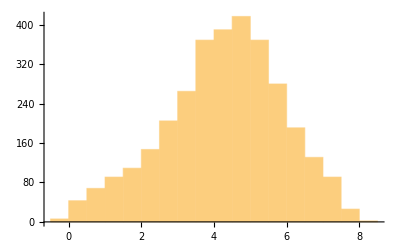

```mathematica
Histogram[ta]
```

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[23.5],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

```mathematica
{Mean[ta2],StandardDeviation[ta2],Kurtosis[ta2]}
```

{0.00765061,0.252976,3.01771}

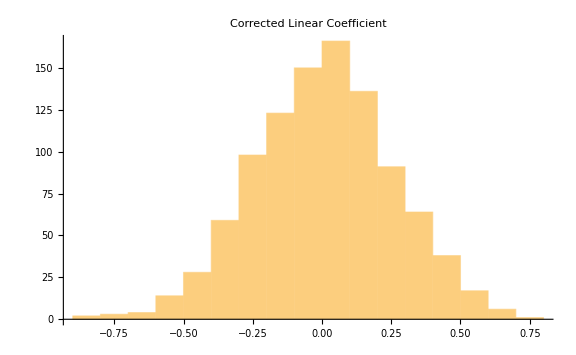

```mathematica
pl2=Histogram[ta2,PlotLabel->"Corrected Linear Coefficient",ImageSize->Large]
```

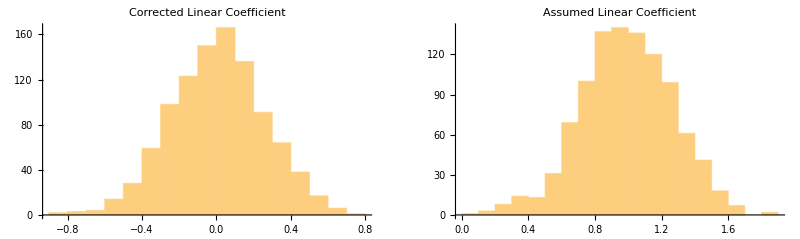

```mathematica
GraphicsGrid[{{pl2,pl1}}]
```

## Trying with low sample size.

https://twitter.com/datepsych/status/1741677937038913931 
The question is, how high is the sample count? This notebook is unfair BECAUSE I am assuming based on the sparseness of the dots, I assume each dot is one sample even though this is unlikely.
Also p-values seem to be totally useless. You run a Monte Carlo simulation, you can get any p-value you want!

-Graphics-

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,7,1}]
```

{1,2,3,4,5,6,7}

We do not have the total sample count. In reality, I suspect only 32 surveys were done.

```mathematica
Y={2,2,5, 8, 9, 4, 2}
```

{2,2,5,8,9,4,2}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution. I doubt that there are actually 32 points.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

```mathematica
Histogram[ta,10,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Amount of Muscularity (1-7)","Probability"},ImageSize->Large]
```

-Graphics-

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{4.25,2.8088,-0.242821}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{-0.319444,-0.242821}

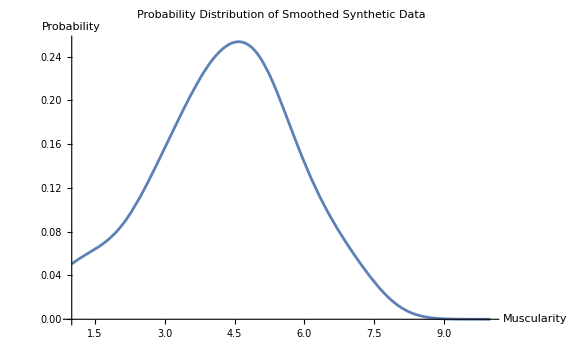

```mathematica
Plot[PDF[dist2,x],{x,1,10},PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity","Probability"},ImageSize->Large]
```

Muscularity of individuals apparently follow a normal distribution

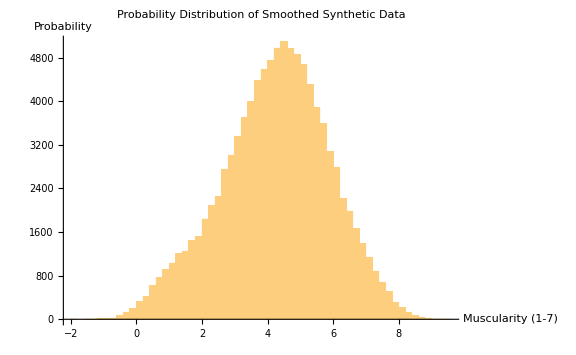

```mathematica
Histogram[RandomVariate[dist2,10^5],50,PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity (1-7)","Probability"},ImageSize->Large]
```

### Testing with No Noise

We find the gradient of a line.

```mathematica
(37-30)/7
```

1

From the picture of the graph, we derive this linear fit.

```mathematica
f=a*x+b/.{a->1,b->30};
```

Apply the regression line to the original function.

```mathematica
f1=f/.x->ta;
```

```mathematica
reg=Transpose[{ta,f1}];
```

```mathematica
lm=LinearModelFit[reg,{1,x},x];
```

Recall the table above was to get this linear regression fit of R^2=1 given the coefficients.

```mathematica
lm
```

FittedModel[30.+1. x]

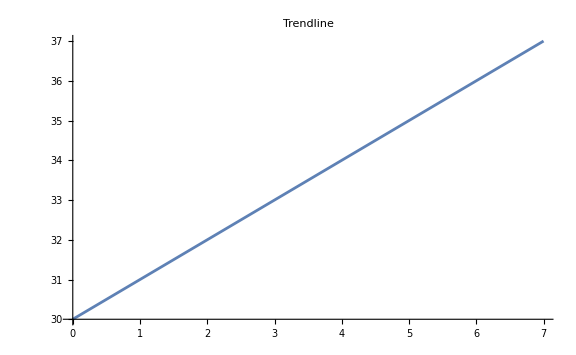

```mathematica
Plot[lm[x],{x,0,7},PlotLabel->"Trendline",ImageSize->Large]
```

Obtain the length of f1 based on the length of samples in ta.

```mathematica
f1//Length
```

32

Apply some Gaussian noise to the function. Then perform the transpose to make it suitable for regression again.

```mathematica
reg1[sigma_]:=Transpose[{ta,f1+RandomVariate[NormalDistribution[0,sigma],Length[f1]]}]
```

Then, apply a linear model fit with the model. Check the p-value as usual, run about the model 10^4 times so as to get a distribution of possible p-values. This is the Monte Carlo simulation for possible p-value given a particular noise and eats up a lot of time. I have calibrate the noise so as to get the supposed p-value.

```mathematica
res=Table[lm=LinearModelFit[reg1[2.225],{1,x},x];lm["ParameterPValues"][[2]],{z,1,10^3}];
```

Get the assumed p-value distribution and parameters.

```mathematica
{Mean[res],StandardDeviation[res],Skewness[res],Kurtosis[res]}
```

{0.00900524,0.0335299,10.1085,152.262}

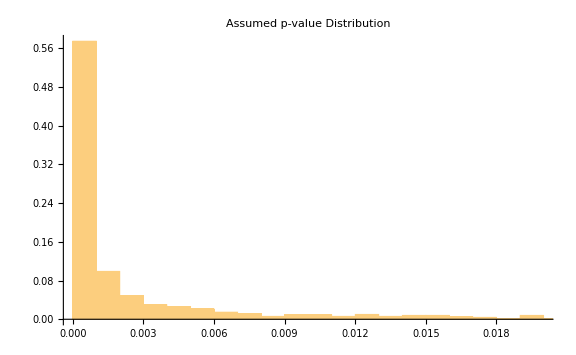

```mathematica
pl0=Histogram[res,Automatic,"Probability",PlotLabel->"Assumed p-value Distribution",ImageSize->Large]
```

Replicate the graph. From the empirical distribution. I now use 32 samples from the dots they had.

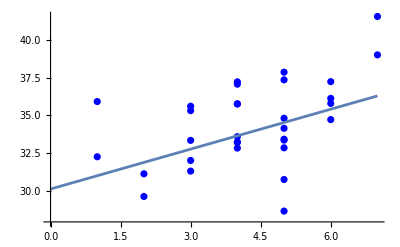

```mathematica
Show[ListPlot[reg1[2.225],PlotStyle->Blue],Plot[lm[x],{x,0,7}]]
```

### Replicating Their Linear Term

Apply the same technique, tabulate the values of the second coefficient, run the Monte Carlo simulation 10^4 times. We use purely the linear term.

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[2.225],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

Get the distribution parameters of the quadratic term.

```mathematica
{Mean[ta2],StandardDeviation[ta2],Skewness[ta2],Kurtosis[ta2]}
```

{0.998736,0.265245,-0.104415,2.98001}

Plot the histogram of the assumed quadratic coefficient.

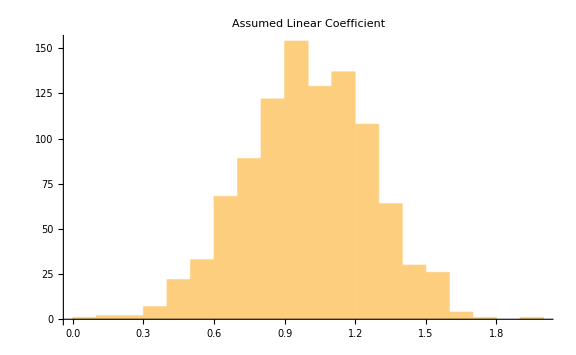

```mathematica
pl1=Histogram[ta2,PlotLabel->"Assumed Linear Coefficient",ImageSize->Large]
```

### Monte-Carlo of both the distribution and the quadratic term.

This is where you get caught out. If you have a low sample count, you should get basically nothing or no correlation. How is it possible that with such a low sample count they got such a distribution?

```mathematica
ta=RandomVariate[dist2,Length[f1]]
```

{4.0164,5.05574,6.35737,5.91735,4.87629,4.40272,4.43228,5.58813,5.13255,4.13296,8.0803,4.67263,3.36837,5.7553,4.17228,4.70837,1.95673,5.00756,5.41325,5.19437,6.89093,7.20488,4.83212,1.87689,5.34338,5.40469,6.02645,3.77788,5.81611,2.85207,3.55917,3.72635}

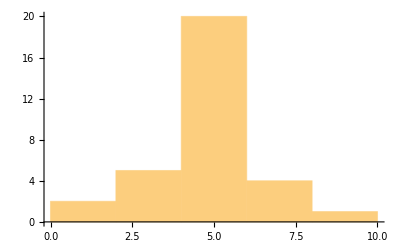

```mathematica
Histogram[ta]
```

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[2.225],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

```mathematica
{Mean[ta2],StandardDeviation[ta2],Kurtosis[ta2]}
```

{-0.179257,0.289457,2.91351}

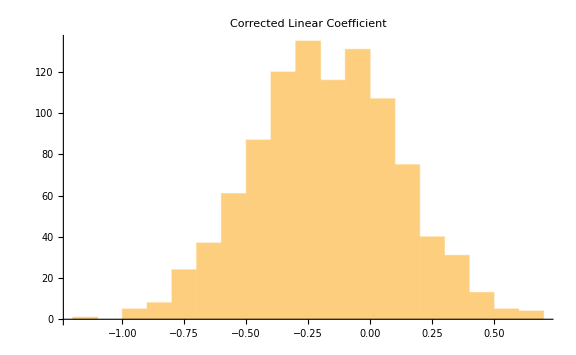

```mathematica
pl2=Histogram[ta2,PlotLabel->"Corrected Linear Coefficient",ImageSize->Large]
```

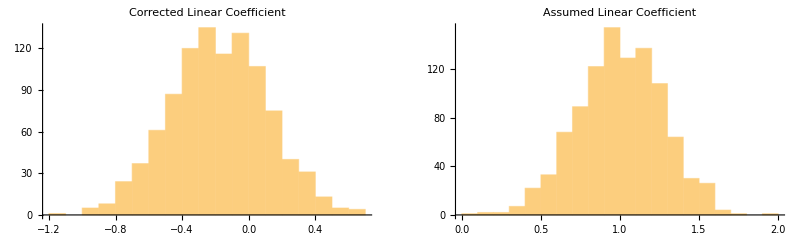

```mathematica
GraphicsGrid[{{pl2,pl1}}]
```